```mathematica
Quit[];
```

```mathematica
here=NotebookDirectory[];
```

```mathematica
PyCodes=here<>"/python_codes";
```

```mathematica
(*$MinPrecision = 50;
SetSystemOptions["CheckMachineUnderflow"->False];*)
```

## Plot Style

```mathematica
MyFont="Times New Roman";
MyLabelSize=17;
MyTickSize=17;
(*MyLegendSize=5;*)
```

```mathematica
MyOptions=Sequence[Frame->True,
GridLinesStyle->Lighter@Lighter@Gray,
LabelStyle->Directive[FontFamily->MyFont,FontSize->MyLabelSize],
FrameStyle->Directive[FontFamily->MyFont,FontSize->MyLabelSize],
FrameTicksStyle->Directive[FontFamily->MyFont,FontSize->MyTickSize]];
```

## Definitions

```mathematica
ClearAll[K1,K2,Kratio, Yz,YzInt,nz,nzInt,gStar,gStar Interp];

K1=Import["/home/michele/Documents/Projects/Quintuplet/python_codes/K1_hiprec.txt","Table"];
K1={K1[[All,1]],10^K1[[All,2]]}//Transpose;

K2=Import["/home/michele/Documents/Projects/Quintuplet/python_codes/K2_hiprec.txt","Table"];
K2={K2[[All,1]],10^K2[[All,2]]}//Transpose;

Kratio[z_] = Interpolation[{K1[[All,1]],(K1/K2)[[All,2]]}//Transpose][z];

Yz = Import["/home/michele/Documents/Projects/Quintuplet/python_codes/YDMeq_z.txt","Table"];
(*Yz={Yz[[All,1]],10^Yz[[All,2]]}//Transpose;*)
YzInt[z_]= Interpolation[Yz][z];

nz = Import["/home/michele/Documents/Projects/Quintuplet/python_codes/nDMeq_z.txt","Table"];
nzInt[z_]= Interpolation[nz][z];

gStar = Import[PyCodes<>"/sqrtgsT.csv","Data"];
gStar Interp[x_] = Interpolation[gStar,InterpolationOrder->1][x];
```

```mathematica
Last@K1
```

{1.×10^7,6.0121171826×10^-4342949}

```mathematica
gSMall = 106.75 ;(* SM degrees of freedom at T > MZ *)

MPl = 1.22 10^19 ;(* Plank mass in GeV *)

g2MZ = 0.6  ;α2MZ =(* g2MZ^2/(4π)*)0.0313;(* Approximate SU(2) gauge coupling at MZ *)

TeV = 10^3;

eV = 10^-9;

ng=3; 

mZfix = 91;μW = 163;

(* Impose scan range *)
zmin = 10;zmax = 10^5; steps = 50;

(* Impose Quintuplet of SU(2) *)
TR = 10;dR = 5; dadj = 9;

(* List of Masses to scan *)
MχList =Table[i,{i,3,14,.2}];
```

```mathematica
(* Thermal W mass and vev *)
Clear[Tc,Rvev,vevT,MWSU2,MWTSU2];

vev=246.;MZ=91.187;MW=80.38;Tc=155.;

Rvev[Mχ_,z_]:=Re[Sqrt[1-(Mχ/z)^2/Tc^2]];
vevT[Mχ_,z_]:=vev*Rvev[Mχ,z];

MWSU2[Mχ_,z_] :=√(11/6 (Mχ/z)^2 α2MZ 4 π);

MWTSU2[Mχ_,z_]:=√(MW^2 Rvev[Mχ,z]^2 +MWSU2[Mχ,z]^2);
```

```mathematica
(* Lists of quantum numbers  *)
Qs1={0,5};
Qp3={3,5};
Qp1={1,5};Qp5={5,5};Qp7={7,5};Qp9={9,5};

Qqn = {Qs1,Qp1,Qp3,Qp5,Qp7,Qp9};

s11={1,5};
s13={3,5};
s15 = {5,5};
gI 1s={1,9,5};


gI 2p = {3,3,15};

BSqn = {s11,s13,s15};
```

### Degrees of freedom vs T

```mathematica
Clear[ρFeq,nFeq,sFeq];Exp5=Exp[5.];
lρFeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(2 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]+1)e^2,{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];
lnFeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(2 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]+1)e,{e,1,1+20/mT}]]},{lmT,-5,5,0.02}],InterpolationOrder->3];
lsFeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(6 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]+1)(4 e^2-1),{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];  
ρFeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,(7 π^2)/240 T^4,T<m/Exp5,m((m T)/(2π))^(3/2)Exp[-m/T],True, m^4 Exp[lρFeq[Log[m/T]]]];
nFeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,3/4 Zeta[3]/π^2 T^3,T<m/Exp5, ((m T)/(2π))^(3/2)Exp[-m/T](1+(15 T)/(8 m)),True, m^3 Exp[lnFeq[Log[m/T]]]];
sFeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,4/3 7/8 π^2/30 T^3,T<m/Exp5, (m+T)/T ((m T)/(2π))^(3/2)Exp[-m/T],True, m^4/T Exp[lsFeq[Log[m/T]]]];
```

```mathematica
Clear[ρBeq,nBeq,sBeq];
lρBeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(2 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]-1)e^2,{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];
lnBeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(2 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]-1)e,{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];
lsBeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(6 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]-1)(4 e^2-1),{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];
ρBeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,π^2/30 T^4,T<m/Exp5,m((m T)/(2π))^(3/2)Exp[-m/T],True, m^4 Exp[lρBeq[Log[m/T]]]];
nBeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,Zeta[3]/π^2 T^3,T<m/Exp5, ((m T)/(2π))^(3/2)Exp[-m/T],True, m^3 Exp[lnBeq[Log[m/T]]]];
sBeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,4/3 π^2/30 T^3,T<m/Exp5,(m+T)/T ((m T)/(2π))^(3/2)Exp[-m/T],True, m^4/T Exp[lsBeq[Log[m/T]]]];
```

```mathematica
Clear[ΓT,sSM,ρSM,YTeq,z,ρR,T,H,ρSM,sSM];
gSM=ndofSM=2(8+3+1)+7/8(3 15 2)+4.;
ndofMSSM=(2 7/8+2)(8+3+1+3 15+4);
```

```mathematica
MZ=91.1875;MW=80.38;MHiggs=125;Mgluon=0.3;
Mto=171;Mbo=4;Mτ=1.77;
Mch=1.3;Ms=0.17;Mμ=0.105;
Mup=0.3;Mdw=0.3;Me=0.511/1000;
Clear[gSMT,T];
gSMT[T_]:=(2+7/8 3 2 )+(sBeq[MHiggs,T]+3 sBeq[MZ,T]+6sBeq[MW,T]+16 sBeq[Mgluon,T]+(12(sFeq[Mto,T]+sFeq[Mbo,T]+sFeq[Mch,T]+sFeq[Ms,T]+sFeq[Mup,T]+sFeq[Mdw,T])+4 (sFeq[Mτ,T]+sFeq[Mμ,T]+sFeq[Me,T])))/(4/3 π^2/30 T^3);
gSMTI=Interpolation[Table[{10^lT,gSMT[10^lT]},{lT,-4,9,0.05}]];//Quiet
```

```mathematica
dgSMTI=Interpolation[Table[{10^lT,10^lT gSMTI'[10^lT]/gSMT[10^lT]},{lT,-4,9,0.05}]];//Quiet
```

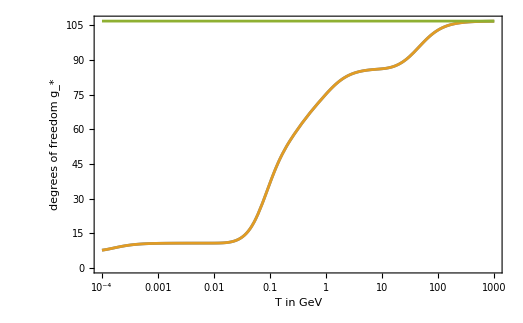

```mathematica
fig=LogLinearPlot[{gSMT[T],gSMTI[T],ndofSM(*,gStar Interp[T]*)},{T,10^-4,10^3},FrameLabel->{"T in GeV","degrees of freedom g_*"},Evaluate[MyOptions]]//Quiet
```

## Check

## Hulten case

### Define basic quantities

```mathematica
ClearAll[z,YDMEQ,σ0,λBEFactor,αeff,λeff,EB1, entropy, Hubble,YIeq,nDMeq,nIeq];

κ = 1.74;

entropy[Mχ_,z_]:=(2 π^2)/45 gSMTI[Mχ/z] (Mχ/z)^3;

Hubble[Mχ_,z_]:=2 √(π^3/45 gSMTI[Mχ/z]) (Mχ^2/(z^2 MPl));

(* DM number density *)
nDMeq[Mχ_,z_]:=gχ Mχ^3/(2π)^(3/2)10^nzInt[z]/.gχ->10 ;

YDMEQ[Mχ_,z_]:=((gχ 45)/((2π)^(3/2) 2 π^2 gSMTI[Mχ/z])) 10^YzInt[z]/.gχ->10 ;

(* equilibrium abundance of DM *)

σ0[Mχ_]:=(π α2MZ^2)/Mχ^2 (207/20); (* s-wave cross section for quintuplet *)
σ0prime[Mχ_]:=(π α2MZ^2)/Mχ^2;

λBEFactor[Mχ_]:=√((gSMall π)/45)σ0prime[Mχ] MPl Mχ;

λeff[{Isp_,n_}]:=(2 n^2 - 1 - Isp^2)/8;

αeff[{Isp_,n_}]:=α2MZ λeff[{Isp,n}] ;

EB1[Mχ_,{Isp_,nS_},nE_,l_,z_]:=αeff[{Isp,nS}]^2/(4 nE^2)(1 - nE^2(κ MWTSU2[Mχ,z])/(αeff[{Isp,nS}] Mχ) - 0.53 nE^2((κ MWTSU2[Mχ,z])/(αeff[{Isp,nS}] Mχ))^2 l (l+1))^2; (* Binding energy for Coulomb potential *)

(* BS number density*) nIeq[Mχ_,z_,gI_,{IspF_,nF_},nE_,l_]:=gI ( (2 Mχ^2/z)/(2π))^(3/2)Exp[-(2 - EB1[Mχ,{IspF,nF},nE,l,z]) z];

YIeq[Mχ_,z_,gI_,{Isp_,n_},nE_,l_]:=nIeq[Mχ,z,gI,{Isp,n},nE,l]/entropy[Mχ,z];

ΩDM[h_,YDMInf_,Mχ_]:=((.11)/h^2) ((YDMInf Mχ)/(.4 eV));
```

### DM annihilation rate without Sommerfeld

```mathematica
ClearAll[NoSommerfeldTAfromPy,NoSommerfeldTAS1,NoSommerfeldTAS3,NoSommerfeldTAS5,NoSommerfeldHulten];

NoSommerfeldTAfromPy = Import[PyCodes<>"/NoSommTA.txt","Table"];

NoSommerfeldTAS1[ϵ_,z_] =Interpolation[{NoSommerfeldTAfromPy[[All,1]],NoSommerfeldTAfromPy[[All,2]],NoSommerfeldTAfromPy[[All,3]]}//Transpose,InterpolationOrder->1][ϵ,z];
NoSommerfeldTAS3[ϵ_,z_] =Interpolation[{NoSommerfeldTAfromPy[[All,1]],NoSommerfeldTAfromPy[[All,2]],NoSommerfeldTAfromPy[[All,4]]}//Transpose,InterpolationOrder->1][ϵ,z];
NoSommerfeldTAS5[ϵ_,z_] =Interpolation[{NoSommerfeldTAfromPy[[All,1]],NoSommerfeldTAfromPy[[All,2]],NoSommerfeldTAfromPy[[All,5]]}//Transpose,InterpolationOrder->1][ϵ,z];

NoSommerfeldHulten[Qp3] =Table[{Mχ TeV,σ0[Mχ TeV]10^NoSommerfeldTAS3[MWTSU2[Mχ TeV,z]/(αeff[Qp3] Mχ TeV),z]},{Mχ,MχList}];
NoSommerfeldHulten[Qp1] =Table[{Mχ TeV,σ0[Mχ TeV]10^NoSommerfeldTAS1[MWTSU2[Mχ TeV,z]/(αeff[Qp1] Mχ TeV),z]},{Mχ,MχList}];
NoSommerfeldHulten[Qp5] =Table[{Mχ TeV,σ0[Mχ TeV]10^NoSommerfeldTAS5[MWTSU2[Mχ TeV,z]/(αeff[Qp5] Mχ TeV),z]},{Mχ,MχList}];
```

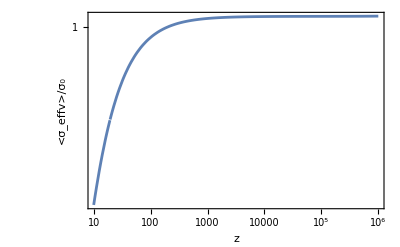

```mathematica
LogLogPlot[{NoSommerfeldHulten[Qp3][[1,2]]/σ0[3 TeV]},{z,10,10^6},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"}]
```

```mathematica
σvNoSommerfeldHulten =NoSommerfeldHulten[Qp3];
```

### DM annihilation rate with Huelten Sommerfeld effect

```mathematica
ClearAll[SommerfeldHueltenTAfromPy,SommerfeldHulten];

SommerfeldHueltenTAfromPy = Import[PyCodes<>"/SommHueltenTA.txt","Table"];

SommerfeldHueltenTAS1[ϵ_,z_] =Interpolation[{SommerfeldHueltenTAfromPy[[All,1]],SommerfeldHueltenTAfromPy[[All,2]],SommerfeldHueltenTAfromPy[[All,3]]}//Transpose,InterpolationOrder->2][ϵ,z];

SommerfeldHueltenTAS3[ϵ_,z_] =Interpolation[{SommerfeldHueltenTAfromPy[[All,1]],SommerfeldHueltenTAfromPy[[All,2]],SommerfeldHueltenTAfromPy[[All,4]]}//Transpose,InterpolationOrder->2][ϵ,z];

SommerfeldHueltenTAS5[ϵ_,z_] =Interpolation[{SommerfeldHueltenTAfromPy[[All,1]],SommerfeldHueltenTAfromPy[[All,2]],SommerfeldHueltenTAfromPy[[All,5]]}//Transpose,InterpolationOrder->2][ϵ,z];

SommerfeldHulten[Qp1] =Table[{MχList[[i]] TeV,σ0[MχList[[i]] TeV]10^SommerfeldHueltenTAS1[(κ MWTSU2[MχList[[i]] TeV,z])/(αeff[Qp1] MχList[[i]] TeV),z]},{i,Length@MχList}];
SommerfeldHulten[Qp3] =  Table[{MχList[[i]] TeV,σ0[MχList[[i]] TeV]10^SommerfeldHueltenTAS3[(κ MWTSU2[MχList[[i]] TeV,z])/(αeff[Qp3] MχList[[i]] TeV),z]},{i,Length@MχList}];
SommerfeldHulten[Qp5] =Table[{MχList[[i]] TeV,σ0[MχList[[i]] TeV]10^SommerfeldHueltenTAS5[(κ MWTSU2[MχList[[i]] TeV,z])/(αeff[Qp5]MχList[[i]] TeV),z]},{i,Length@MχList}];

SommerfeldHultenMassless[Qp1] =Table[{Mχ TeV,σ0[Mχ TeV]10^SommerfeldHueltenTAS1[0,z]},{Mχ,MχList}];
```

```mathematica
(* DM annihilation rates *)

σvHultenSE[QList_, wQList_]:=Sum[wQList[[j]]SommerfeldHulten[QList[[j]]],{j,Length@QList}];
```

```mathematica
σvHultenSESW =σvHultenSE[{Qp1, Qp3, Qp5},{16/69,25/69, 28/69}];
```

```mathematica
σvHultenSESW//Length
```

56

```mathematica
aa = σvHultenSESW[[1,2]]/σ0[3 TeV];
aa1 = σvHultenSESW[[56,2]]/σ0[14 TeV];
```

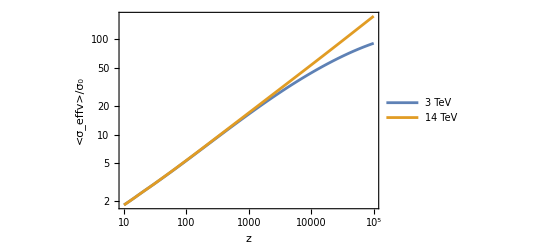

```mathematica
LogLogPlot[{aa,aa1},{z,zmin,zmax},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"},PlotLegends->{"3 TeV","14 TeV"}]
```

### DM annihilation rate with Massless Sommerfeld effect

```mathematica
ClearAll[SommerfeldMassless];

SommerfeldMassless[Qp1] =Table[{Mχ TeV,σ0[Mχ TeV]10^SommerfeldHueltenTAS1[0,z]},{Mχ,MχList}];

SommerfeldMassless[Qp3] =  Table[{Mχ TeV,σ0[Mχ TeV]10^SommerfeldHueltenTAS3[0,z]},{Mχ,MχList}];

SommerfeldMassless[Qp5] =Table[{Mχ TeV,σ0[Mχ TeV]10^SommerfeldHueltenTAS5[0,z]},{Mχ,MχList}];
```

```mathematica
(* DM annihilation rates *)

σvMasslessSE[QList_, wQList_]:=Sum[wQList[[j]]SommerfeldMassless[QList[[j]]],{j,Length@QList}];
```

```mathematica
σvMasslessSESW =σvMasslessSE[{Qp1, Qp3, Qp5},{16/69,25/69, 28/69}];
```

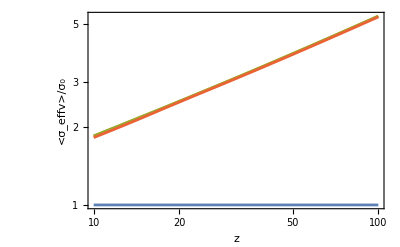

```mathematica
LogLogPlot[{1,(First@σvMasslessSESW)[[2]]/σ0[3 TeV],(Last@σvMasslessSESW)[[2]]/σ0[14 TeV],aa},{z,10,10^2},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"}]
```

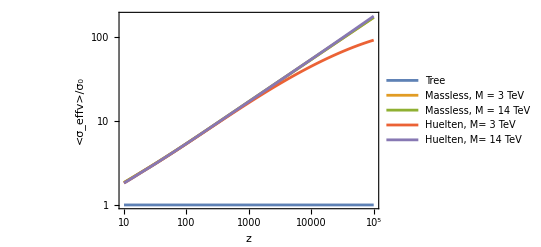

```mathematica
LogLogPlot[{1,(First@σvMasslessSESW)[[2]]/σ0[3 TeV],(Last@σvMasslessSESW)[[2]]/σ0[14 TeV],aa,aa1},{z,10,10^5},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"},PlotLegends->{"Tree","Massless, M = 3 TeV","Massless, M = 14 TeV","Huelten, M= 3 TeV","Huelten, M= 14 TeV"}]
```

### DM Bound state formation

#### Expansion for λ_i=0

```mathematica
(Series[λi (λf ζ)^5 (1/gχ^2) ((2^11 π(1 + ζ^2 λi^2)Exp[-4 ζ λi ArcCot[ζ λf]])/(3 (1 + ζ^2 λf^2)^3(1 - Exp[-2π ζ λi])))(CJ + Cτ/λf)^2,{λi,0,0}]//Normal)/.λf->3/.gχ->10
```

(2304 (3 CJ+Cτ)^2 ζ^4)/(25 (1+9 ζ^2)^3)

```mathematica
(Series[λi (λf ζ)^5 (1/gχ^2) ((2^14 π (*ζ^5*)(1 + ζ^2 λi^2)Exp[-4 ζ λi ArcCot[ζ λf/2]])/(3 (4 + ζ^2 λf^2)^5(1 - Exp[-2π ζ λi])))(CJ(ζ^2 λf(λf-2 λi) - 4) + Cτ(ζ^2 (3 λf-4 λi) - 4/λf))^2,{λi,0,0}]//Normal)/.λf->3/.gχ->10
```

(18432 ζ^4 (-12 CJ-4 Cτ+27 CJ ζ^2+27 Cτ ζ^2)^2)/(25 (4+9 ζ^2)^5)

```mathematica
(Series[λi (λf ζ)^5 (3/gχ^2) ((2^12 π α ζ^2 Exp[-4 ζ λi ArcCot[ζ λf/2]])/(9 (4 + ζ^2 λf^2)^5(1 - Exp[-2π ζ λi])))((CJ (λf(ζ^2 λi (3λf-4λi) + 8) - 12λi) + Cτ(ζ^2(-3 λf^2 + 12 λi λf - 8 λi^2) + 4))^2 + 2^5(ζ^2 λi^2+1)(ζ^2 λi^2+4)(CJ λf+2Cτ)^2),{λi,0,0}]//Normal)/.λf->3/.gχ->10
```

(41472 α ζ^6 (128 (3 CJ+2 Cτ)^2+(24 CJ+Cτ (4-27 ζ^2))^2))/(25 (4+9 ζ^2)^5)

#### 1s

```mathematica
ClearAll[BSF 1s1 TAfromPy,BSF 1s3 TAfromPy,BSF 1s5 TAfromPy,BSF 1s1 TA,BSF 1s3 TA,BSF 1s5 TA,BSF 1s TA List];

BSF 1s1 TAfromPy = Import[PyCodes<>"/BSF_1s1_TA.txt","Table"];
BSF 1s3 TAfromPy = Import[PyCodes<>"/BSF_1s3_TA.txt","Table"];
BSF 1s5 TAfromPy = Import[PyCodes<>"/BSF_1s5_TA.txt","Table"];

BSF 1s1 TA[z_]=10^Interpolation[BSF 1s1 TAfromPy,InterpolationOrder->1][z];
BSF 1s3 TA[z_]=10^Interpolation[BSF 1s3 TAfromPy,InterpolationOrder->1][z];
BSF 1s5 TA[z_]=10^Interpolation[BSF 1s5 TAfromPy,InterpolationOrder->1][z];

BSF 1s TA List= {BSF 1s1 TA[z],BSF 1s3 TA[z],BSF 1s5 TA[z]};
```

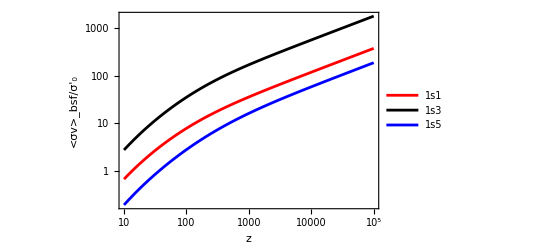

```mathematica
LogLogPlot[{BSF 1s1 TA[z],BSF 1s3 TA[z],BSF 1s5 TA[z]},{z,zmin,zmax},PlotStyle->{Red,Black,Blue},PlotLegends->{"1s1","1s3","1s5"},Evaluate[MyOptions],FrameLabel->{"z","<σv>_bsf/σ'_0"}]
```

```mathematica
LogLogPlot[{BSF 1s1 TA[z],BSF 1s3 TA[z],BSF 1s5 TA[z]},{z,zmin,zmax},PlotStyle->{Red,Black,Blue},PlotLegends->{"1s1","1s3","1s5"},Evaluate[MyOptions],FrameLabel->{"z","<σv>_bsf/σ'_0"}]
```

-Graphics-

```mathematica
ClearAll[ΓI break 1s, ΓI break 1s NoExp];

ΓI break 1s[Mχ_,z_]:=Table[gχ^2/(2 gI 1s[[j]])Mχ^3(1/(z 4 π))^(3/2) Exp[-EB1[Mχ,BSqn[[j]],1,0,z] z]σ0prime[Mχ]BSF 1s TA List[[j]]/.gχ->10,{j,Length@BSF 1s TA List}];

ΓI break 1s NoExp[Mχ_,z_]:=Table[gχ^2/(2 gI 1s[[j]])Mχ^3(1/(z 4 π))^(3/2) σ0prime[Mχ]BSF 1s TA List[[j]]/.gχ->10,{j,Length@BSF 1s TA List}];
```

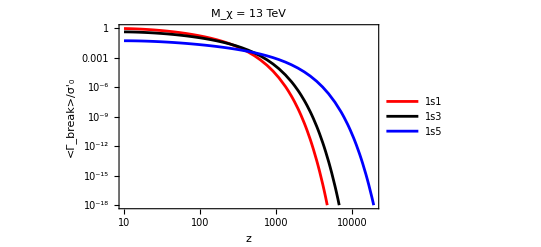

```mathematica
LogLogPlot[{ΓI break 1s[13 TeV,z][[1]],ΓI break 1s[13 TeV,z][[2]],ΓI break 1s[13 TeV,z][[3]]},{z,10,zmax},PlotStyle->{Red,Black,Blue},PlotLegends->{"1s1","1s3","1s5"},Evaluate[MyOptions],PlotRange->{All,{10^-18,1}},FrameLabel->{"z","<Γ_break>/σ'_0"},PlotLabel->"M_χ = 13 TeV"]
```

#### 2s

```mathematica
ClearAll[BSF 2s1 TAfromPy,BSF 2s3 TAfromPy,BSF 2s5 TAfromPy,BSF 2s1 TA,BSF 2s3 TA,BSF 2s5 TA,BSF 2s TA List];

BSF 2s1 TAfromPy = Import[PyCodes<>"/BSF_2s1_TA.txt","Table"];
BSF 2s3 TAfromPy = Import[PyCodes<>"/BSF_2s3_TA.txt","Table"];
BSF 2s5 TAfromPy = Import[PyCodes<>"/BSF_2s5_TA.txt","Table"];

BSF 2s1 TA[z_]=10^Interpolation[BSF 2s1 TAfromPy,InterpolationOrder->1][z];
BSF 2s3 TA[z_]=10^Interpolation[BSF 2s3 TAfromPy,InterpolationOrder->1][z];
BSF 2s5 TA[z_]=10^Interpolation[BSF 2s5 TAfromPy,InterpolationOrder->1][z];

BSF 2s TA List= {BSF 2s1 TA[z],BSF 2s3 TA[z],BSF 2s5 TA[z]};
```

```mathematica
BSF 2s1 TA[100]
```

1.24917446929941

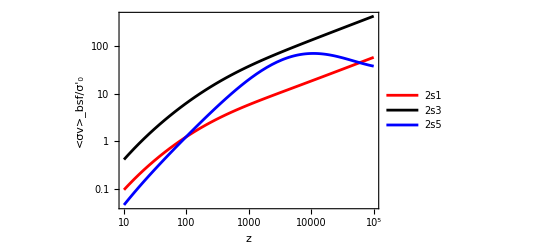

```mathematica
LogLogPlot[{BSF 2s1 TA[z],BSF 2s3 TA[z],BSF 2s5 TA[z]},{z,zmin,zmax},PlotStyle->{Red,Black,Blue},PlotLegends->{"2s1","2s3","2s5"},Evaluate[MyOptions],FrameLabel->{"z","<σv>_bsf/σ'_0"}]
```

```mathematica
ΓI break 2s[Mχ_,z_]:=Table[gχ^2/(2 gI 1s[[j]])Mχ^3(1/(z 4 π))^(3/2) Exp[-EB1[Mχ,BSqn[[j]],2,0,z] z]σ0prime[Mχ]BSF 2s TA List[[j]]/.gχ->10,{j,Length@BSF 2s TA List}];
```

#### 2p

```mathematica
ClearAll[BSF 2p1 TAfromPy,BSF 2p3 TAfromPy,BSF 2p5 TAfromPy,BSF 2p1 TA,BSF 2p3 TA,BSF 2p5 TA,BSF 2p TA List];

BSF 2p1 TAfromPy = Import[PyCodes<>"/BSF_2p1_TA.txt","Table"];
BSF 2p3 TAfromPy = Import[PyCodes<>"/BSF_2p3_TA.txt","Table"];
BSF 2p5 TAfromPy = Import[PyCodes<>"/BSF_2p5_TA.txt","Table"];

BSF 2p1 TA[z_]=10^Interpolation[BSF 2p1 TAfromPy,InterpolationOrder->1][z];
BSF 2p3 TA[z_]=10^Interpolation[BSF 2p3 TAfromPy,InterpolationOrder->1][z];
BSF 2p5 TA[z_]=10^Interpolation[BSF 2p5 TAfromPy,InterpolationOrder->1][z];

BSF 2p TA List= {BSF 2p1 TA[z],BSF 2p3 TA[z],BSF 2p5 TA[z]};
```

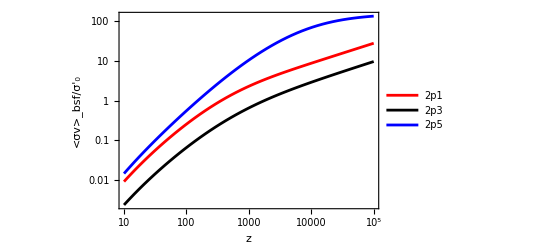

```mathematica
LogLogPlot[{BSF 2p1 TA[z],BSF 2p3 TA[z],BSF 2p5 TA[z]},{z,zmin,zmax},PlotStyle->{Red,Black,Blue},PlotLegends->{"2p1","2p3","2p5"},Evaluate[MyOptions],FrameLabel->{"z","<σv>_bsf/σ'_0"}]
```

```mathematica
ΓI break 2p[Mχ_,z_]:=Table[gχ^2/(2 gI 2p[[j]])Mχ^3(1/(z 4 π))^(3/2) Exp[-EB1[Mχ,BSqn[[j]],2,1,z] z]σ0prime[Mχ]BSF 2p TA List[[j]]/.gχ->10,{j,Length@BSF 2p TA List}];
```

#### Combine plots

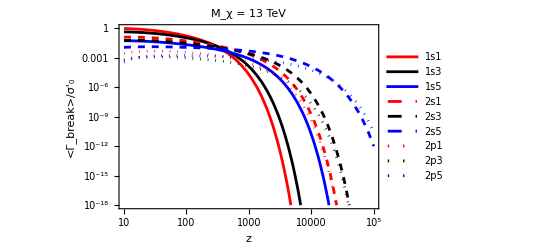

```mathematica
LogLogPlot[{ΓI break 1s[13 TeV,z][[1]],ΓI break 1s[13 TeV,z][[2]],ΓI break 1s[13 TeV,z][[3]],ΓI break 2s[13 TeV,z][[1]],ΓI break 2s[13 TeV,z][[2]],ΓI break 2s[13 TeV,z][[3]],ΓI break 2p[13 TeV,z][[1]],ΓI break 2p[13 TeV,z][[2]],ΓI break 2p[13 TeV,z][[3]]},{z,10,zmax},PlotStyle->{Red,Black,Blue,{Red,Dashed},{Black,Dashed},{Blue,Dashed},{Red,Dotted},{Black,Dotted},{Blue,Dotted}},PlotLegends->{"1s1","1s3","1s5","2s1","2s3","2s5","2p1","2p3","2p5"},Evaluate[MyOptions],PlotRange->{All,{10^-18,1}},FrameLabel->{"z","<Γ_break>/σ'_0"},PlotLabel->"M_χ = 13 TeV"]
```

### Bound state decay rates

```mathematica
ClearAll[Γann Massless,Γann Huelten,Γann Massless TA,Γann Huelten TA,γI ann];

γI ann = α2MZ^5 {3240,15626/48,567/4};

Γann Massless[Mχ_,z_]:=γI ann Mχ;
Γann Huelten[Mχ_,z_]:=γI ann Mχ(1 + (κ^2 MWTSU2[Mχ,z]^2)/(α2MZ^2 Mχ^2));

Γann Massless TA[Mχ_,z_]:=Γann Massless[Mχ,z] Kratio[z];
Γann Huelten TA[Mχ_,z_]:=Γann Huelten[Mχ,z] Kratio[z];

γI ann Massless[Mχ_,z_]:=( (2 Mχ^2/z)/(2π))^(3/2)Exp[-(2 - α2MZ^2/2) z] Γann Massless TA[Mχ,z];
γI ann Huelten[Mχ_,z_]:=( (2 Mχ^2/z)/(2π))^(3/2)Exp[-(2 - α2MZ^2/2) z] Γann Huelten TA[Mχ,z];
```

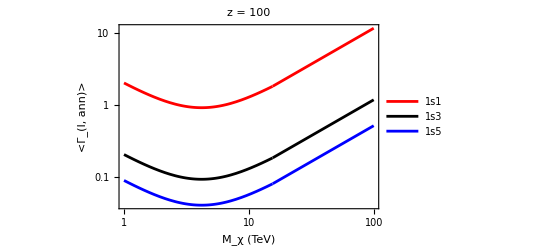

```mathematica
LogLogPlot[{Γann Huelten TA[i TeV,100][[1]],Γann Huelten TA[i TeV,100][[2]],Γann Huelten TA[i TeV,100][[3]]},{i,1,100},PlotStyle->{Red,Black,Blue},PlotLegends->{"1s1","1s3","1s5"},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","<Γ_(I, ann)>"},PlotLabel->"z = 100"]
```

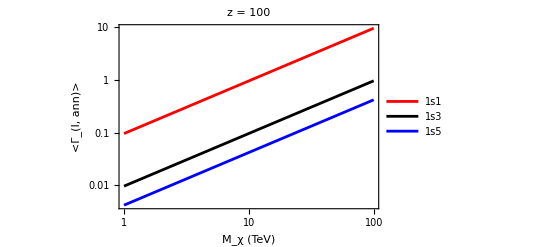

```mathematica
LogLogPlot[{Γann Massless TA[i TeV,100][[1]],Γann Massless TA[i TeV,100][[2]],Γann Massless TA[i TeV,100][[3]]},{i,1,100},PlotStyle->{Red,Black,Blue},PlotLegends->{"1s1","1s3","1s5"},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","<Γ_(I, ann)>"},PlotLabel->"z = 100"]
```

### DM annihilation rate TRIPLET without Sommerfeld

```mathematica
(*ClearAll[TripletNoSommerfeldTAfromPy,TripletNoSommerfeldTAS1,TripletNoSommerfeldTAS3,TripletNoSommerfeldHulten];

TripletNoSommerfeldTAfromPy = Import[PyCodes<>"/NoSommTA_Triplet.txt","Table"];

TripletNoSommerfeldTAS1[ϵ_,z_] =Interpolation[{TripletNoSommerfeldTAfromPy[[All,1]],TripletNoSommerfeldTAfromPy[[All,2]],TripletNoSommerfeldTAfromPy[[All,3]]}//Transpose,InterpolationOrder->1][ϵ,z];
TripletNoSommerfeldTAS3[ϵ_,z_] =Interpolation[{TripletNoSommerfeldTAfromPy[[All,1]],TripletNoSommerfeldTAfromPy[[All,2]],TripletNoSommerfeldTAfromPy[[All,4]]}//Transpose,InterpolationOrder->1][ϵ,z];

TripletNoSommerfeldHulten[Qp3] =Table[{Mχ TeV,σ0[Mχ TeV]10^TripletNoSommerfeldTAS3[-MWTSU2[Mχ TeV,z]/(αeff[Qp3] Mχ TeV),z]},{Mχ,MχList}];
TripletNoSommerfeldHulten[Qp1] =Table[{Mχ TeV,σ0[Mχ TeV]10^TripletNoSommerfeldTAS1[-MWTSU2[Mχ TeV,z]/(αeff[Qp1] Mχ TeV),z]},{Mχ,MχList}];*)
```

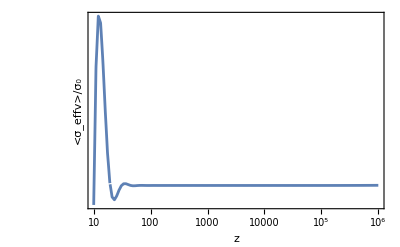

```mathematica
(*LogLogPlot[{TripletNoSommerfeldHulten[Qp3][[1,2]]/σ0[3 TeV]},{z,10,10^6},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"}]*)
```

```mathematica
(*σvTripletNoSommerfeldHulten =TripletNoSommerfeldHulten[Qp3];*)
```

### DM annihilation rate TRIPLET with Huelten Sommerfeld effect

```mathematica
(*ClearAll[TripletSommerfeldHueltenTAfromPy,TripletSommerfeldHulten];

TripletSommerfeldHueltenTAfromPy = Import[PyCodes<>"/SommHueltenTA_Triplet.txt","Table"];

TripletSommerfeldHueltenTAS1[ϵ_,z_] =Interpolation[{TripletSommerfeldHueltenTAfromPy[[All,1]],TripletSommerfeldHueltenTAfromPy[[All,2]],TripletSommerfeldHueltenTAfromPy[[All,3]]}//Transpose,InterpolationOrder->2][ϵ,z];

TripletSommerfeldHueltenTAS3[ϵ_,z_] =Interpolation[{TripletSommerfeldHueltenTAfromPy[[All,1]],TripletSommerfeldHueltenTAfromPy[[All,2]],TripletSommerfeldHueltenTAfromPy[[All,4]]}//Transpose,InterpolationOrder->2][ϵ,z];

TripletSommerfeldHulten[Qp1] =Table[{MχList[[i]] TeV,σ0[MχList[[i]] TeV]10^TripletSommerfeldHueltenTAS1[-MWTSU2[MχList[[i]] TeV,z]/(αeff[Qp1] MχList[[i]] TeV),z]},{i,Length@MχList}];
TripletSommerfeldHulten[Qp3] =  Table[{MχList[[i]] TeV,σ0[MχList[[i]] TeV]10^TripletSommerfeldHueltenTAS3[-MWTSU2[MχList[[i]] TeV,z]/(αeff[Qp3] MχList[[i]] TeV),z]},{i,Length@MχList}];*)
```

```mathematica
(*(* DM annihilation rates *)

σvTripletHultenSE[QList_, wQList_]:=Sum[wQList[[j]]TripletSommerfeldHulten[QList[[j]]],{j,Length@QList}];*)
```

```mathematica
(*σvTripletHultenSESW =σvTripletHultenSE[{Qp1, Qp3},{16/111,20/111, 75/111}];*)
```

```mathematica
(*σvTripletHultenSESW[[1]]*)
```

{1782.61+28/69 TripletSommerfeldHulten[{5,5}],1.0743×10^-9 10^(InterpolatingFunction[…][-0.00232706 √((5.94×10^6)/z^2+6460.94 Re[√(1-374.61/z^2)]^2),z])+6.87549×10^-10 10^(InterpolatingFunction[…][-0.00193922 √((5.94×10^6)/z^2+6460.94 Re[√(1-374.61/z^2)]^2),z])+28/69 TripletSommerfeldHulten[{5,5}]}

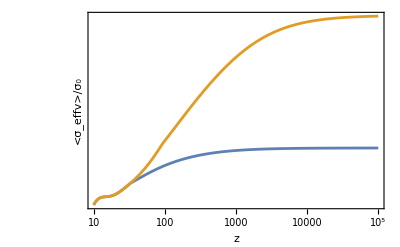

```mathematica
(*LogLogPlot[{aa,aa1},{z,zmin,zmax},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"}]*)
```

### DM annihilation rate TRIPLET with Massless Sommerfeld effect

```mathematica
(*ClearAll[SommerfeldMassless];

SommerfeldMassless[Qp1] =Table[{Mχ TeV,σ0[Mχ TeV]10^SommerfeldHueltenTAS1[0,z]},{Mχ,MχList}];

SommerfeldMassless[Qp3] =  Table[{Mχ TeV,σ0[Mχ TeV]10^SommerfeldHueltenTAS3[0,z]},{Mχ,MχList}];

SommerfeldMassless[Qp5] =Table[{Mχ TeV,σ0[Mχ TeV]10^SommerfeldHueltenTAS5[0,z]},{Mχ,MχList}];*)
```

```mathematica
(*(* DM annihilation rates *)

σvMasslessSE[QList_, wQList_]:=Sum[wQList[[j]]SommerfeldMassless[QList[[j]]],{j,Length@QList}];*)
```

```mathematica
(*σvMasslessSESW =σvMasslessSE[{Qp1, Qp3, Qp5},{16/69,25/69, 28/69}];*)
```

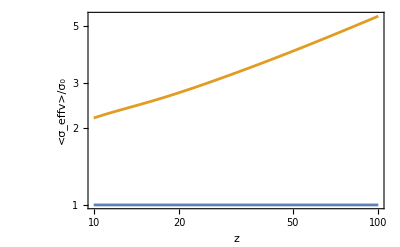

```mathematica
(*LogLogPlot[{1,(First@σvMasslessSESW)[[2]]/σ0[3 TeV](*,(Last@σvMasslessSESW)[[2]]/σ0[14 TeV]*)},{z,10,10^2},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"}]*)
```

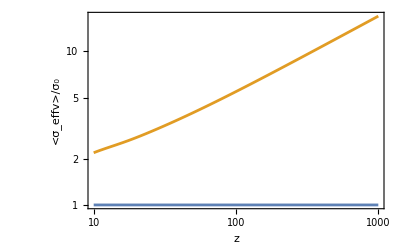

```mathematica
(*LogLogPlot[{1,(Last@σvMasslessSESW)[[2]]/σ0[14 TeV]},{z,10,10^3},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"}]*)
```

```mathematica
(* *)
```

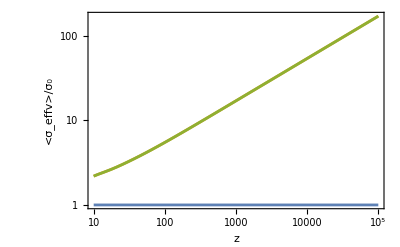

```mathematica
(*LogLogPlot[{1,(First@σvMasslessSESW)[[2]]/σ0[3 TeV],(Last@σvMasslessSESW)[[2]]/σ0[14 TeV]},{z,10,zmax},PlotRange->All,Evaluate[MyOptions],FrameLabel->{"z","<σ_effv>/σ_0"}]*)
```

### Boltzmann Equations

#### Define prefactors

```mathematica
ClearAll[preFactorσ,preFactor I];

Dz[x_]:=D[x[z],z];

preFactor[Mχ_,z_]:=(1/(entropy[Mχ,z] Hubble[Mχ,z] z));
preFactor I[Mχ_,z_]:=(1/(Hubble[Mχ,z] z));

preFactorσ[Mχ_,z_]:=-(entropy[Mχ,z]/(z Hubble[Mχ,z]));
```

#### Define bound states YEQ

```mathematica
YBSEQ[s11][Mχ_,z_]:=YIeq[Mχ,z,gI 1s[[1]],s11,1,0];
YBSEQ[s13][Mχ_,z_]:=YIeq[Mχ,z,gI 1s[[2]],s13,1,0];
YBSEQ[s15][Mχ_,z_]:=YIeq[Mχ,z,gI 1s[[3]],s15,1,0];

nBSEQ[s11][Mχ_,z_]:=nIeq[Mχ,z,s11,1];
nBSEQ[s13][Mχ_,z_]:=nIeq[Mχ,z,s13,1];
nBSEQ[s15][Mχ_,z_]:=nIeq[Mχ,z,s15,1];
```

```mathematica
BSvar={Ys11,Ys13,Ys15};
```

```mathematica
ClearAll[Yratio, Yratio NoExp];

Yratio[Mχ_,z_]:=Table[(gI 1s[[j]] gSMTI[Mχ/z])/gχ^2((π^(5/2) 32)/45) (Exp[z EB1[Mχ,BSqn[[j]],1,0,z]]/z^(3/2))/.gχ->10,{j,Length@gI 1s}];

Yratio NoExp[Mχ_,z_]:=Table[(gI 1s[[j]] gSMTI[Mχ/z])/gχ^2((π^(5/2) 32)/45) (1/z^(3/2))/.gχ->10,{j,Length@gI 1s}];
```

#### Boltzmann RHS - No Sommerfeld and No BS

```mathematica
ClearAll[χBoltzNoSommRHS,SolutionNoSomm];

χBoltzNoSommRHS= Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z]σvNoSommerfeldHulten[[i,2]] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) },{i,Length@MχList}];

SolutionNoSomm[i_]:= {MχList[[i]] TeV,NDSolve[{D[YDM[z],z]==χBoltzNoSommRHS[[i,2]],YDM[zmin]==1.00001YDMEQ[MχList[[i]] TeV,zmin]},YDM,{z,zmin,zmax},Method->"BDF"(*,Method->"StiffnessSwitching"*)(*,WorkingPrecision->30*),AccuracyGoal->20][[1]]}//Quiet;
```

```mathematica
ListYieldsHultenNoSommNoBS = Table[SolutionNoSomm[i],{i,1,11}];//AbsoluteTiming
```

{1.11063,Null}

```mathematica
ListSolutionHultenNoSommNoBS = Select[{ListYieldsHultenNoSommNoBS[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYieldsHultenNoSommNoBS[[All,2]]),ListYieldsHultenNoSommNoBS[[All,1]]]}//Transpose,#[[2]]>0 &];//Quiet
```

```mathematica
FindRoot[Interpolation[ListSolutionHultenNoSommNoBS][x] == 0.1198,{x,5}]
```

{x→3.97836}

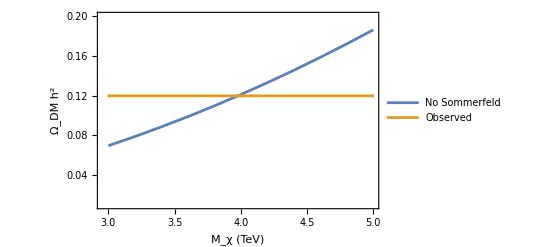

```mathematica
ListPlot[{ListSolutionHultenNoSommNoBS,Table[{i,Around[.1198,.0017]},{i,3,5}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

#### Boltzmann RHS - Massless Sommerfeld and No BS

```mathematica
ClearAll[χBoltzRHSnoBS,SolutionMasslessNoBS];

χBoltzRHSnoBS = Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z]σvMasslessSESW[[i,2]] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) },{i,Length@MχList}];

SolutionMasslessNoBS[i_]:={MχList[[i]] TeV,NDSolve[{D[YDM[z],z]==χBoltzRHSnoBS[[i,2]],YDM[zmin]==1.00001YDMEQ[MχList[[i]] TeV,zmin]},YDM,{z,zmin,zmax},Method->"StiffnessSwitching",AccuracyGoal->20][[1]]}//Quiet;
```

```mathematica
ListYieldsMasslessNoBS = Table[SolutionMasslessNoBS[i],{i,1,Length@MχList}];//AbsoluteTiming
```

{15.3451,Null}

```mathematica
YDM[zmax]/.ListYieldsMasslessNoBS[[11,2]]
```

2.5332×10^-14

```mathematica
ListSolutionMasslessNoBS = {ListYieldsMasslessNoBS[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYieldsMasslessNoBS[[All,2]]),ListYieldsMasslessNoBS[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolutionMasslessNoBS][x] == 0.1198,{x,9}]
```

{x→9.42923}

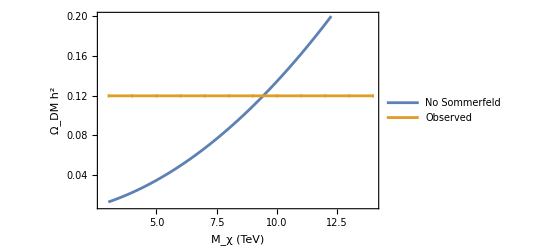

```mathematica
ListPlot[{ListSolutionMasslessNoBS,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

#### Boltzmann RHS - Huelten Sommerfled and No BS

```mathematica
ClearAll[χBoltzRHSnoBS,SolutionHultenNoBS];

χBoltzRHSnoBS = Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z]σvHultenSESW[[i,2]] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) },{i,Length@MχList}];

SolutionHultenNoBS[i_]:={MχList[[i]] TeV,NDSolve[{D[YDM[z],z]==χBoltzRHSnoBS[[i,2]],YDM[zmin]==1.00001YDMEQ[MχList[[i]] TeV,zmin]},YDM,{z,zmin,zmax},Method->"StiffnessSwitching",AccuracyGoal->20][[1]]}//Quiet;
```

```mathematica
ListYieldsHultenNoBS = Table[SolutionHultenNoBS[i],{i,1,Length@MχList}];//AbsoluteTiming
```

{20.5153,Null}

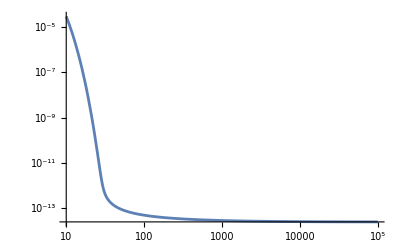

```mathematica
LogLogPlot[YDM[z]/.ListYieldsHultenNoBS[[11,2]],{z,zmin,zmax},PlotRange->All]
```

```mathematica
YDM[zmax]/.ListYieldsHultenNoBS[[All,2]]
```

{1.60387×10^-14,1.68138×10^-14,1.75757×10^-14,1.84271×10^-14,1.92789×10^-14,2.03584×10^-14,2.13776×10^-14,2.22316×10^-14,2.32062×10^-14,2.43482×10^-14,2.54599×10^-14,2.65416×10^-14,2.75764×10^-14,2.85717×10^-14,2.95314×10^-14,3.04584×10^-14,3.1349×10^-14,3.21641×10^-14,3.30011×10^-14,3.38894×10^-14,3.48052×10^-14,3.56763×10^-14,3.65662×10^-14,3.74247×10^-14,3.83446×10^-14,3.92926×10^-14,4.02968×10^-14,4.13164×10^-14,4.23294×10^-14,4.334×10^-14,4.43465×10^-14,4.53334×10^-14,4.62959×10^-14,4.7242×10^-14,4.81784×10^-14,4.9106×10^-14,5.00087×10^-14,5.09068×10^-14,5.18125×10^-14,5.27266×10^-14,5.36655×10^-14,5.46151×10^-14,5.55468×10^-14,5.64705×10^-14,5.73871×10^-14,5.82976×10^-14,5.91872×10^-14,6.0068×10^-14,6.09414×10^-14,6.18276×10^-14,6.27279×10^-14,6.36601×10^-14,6.46108×10^-14,6.55687×10^-14,6.65214×10^-14,6.74578×10^-14}

```mathematica
ListSolutionHultenNoBS = {ListYieldsHultenNoBS[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYieldsHultenNoBS[[All,2]]),ListYieldsHultenNoBS[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolutionHultenNoBS][x] == 0.1198,{x,11}]

FindRoot[Interpolation[ListSolutionHultenNoBS][x] == 0.12,{x,11}]
```

{x→9.40499}

{x→9.41297}

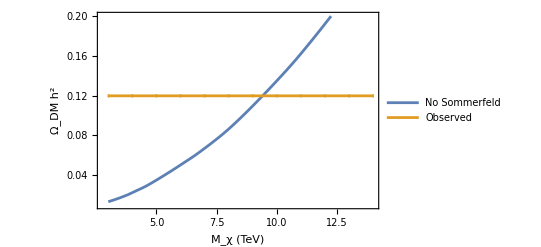

```mathematica
ListPlot[{ListSolutionHultenNoBS,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

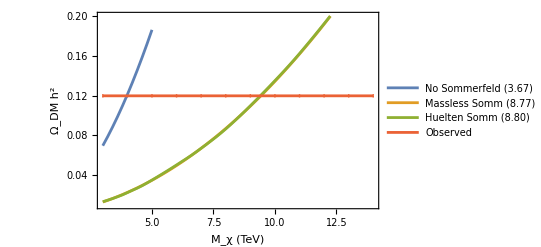

```mathematica
ListPlot[{ListSolutionHultenNoSommNoBS,ListSolutionMasslessNoBS,ListSolutionHultenNoBS,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{{3,14},{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld (3.67)","Massless Somm (8.77)","Huelten Somm (8.80)","Observed"}]
```

#### Boltzmann RHS - with 1s1 BS (effective case)

```mathematica
ClearAll[σveff];σveff[i_] := σvHultenSESW[[i,2]]+σ0prime[MχList[[i]] TeV] (1/(BSF 1s TA List[[1]])+(gχ^2 σ0prime[MχList[[i]] TeV] (MχList[[i]] TeV)^2)/(2gI 1s[[1]] γI ann[[1]])(1/(4π z))^(3/2)Exp[-z EB1[MχList[[i]] TeV,BSqn[[1]],1,0,z]])^-1/.gχ->10;
```

```mathematica
ClearAll[χBoltzRHS BS eff,Solution BS eff];

χBoltzRHS BS eff = Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z]σveff[i] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) },{i,Length@MχList}];

Solution BS eff[i_]:={MχList[[i]] TeV,NDSolve[{D[YDM[z],z]==χBoltzRHS BS eff[[i,2]],YDM[zmin]==1.00001YDMEQ[MχList[[i]] TeV,zmin]},YDM,{z,zmin,zmax},Method->"StiffnessSwitching",AccuracyGoal->20][[1]]}//Quiet;
```

```mathematica
ListYields BS eff = Table[Solution BS eff[i],{i,1,Length@MχList}];//AbsoluteTiming
```

{25.3565,Null}

```mathematica
ListSolution 1s1BS eff = {ListYields BS eff[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYields BS eff[[All,2]]),ListYields BS eff[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolution 1s1BS eff][x] == 0.1198,{x,11}]

FindRoot[Interpolation[ListSolution 1s1BS eff][x] == 0.12,{x,11}]
```

{x→10.0026}

{x→10.0112}

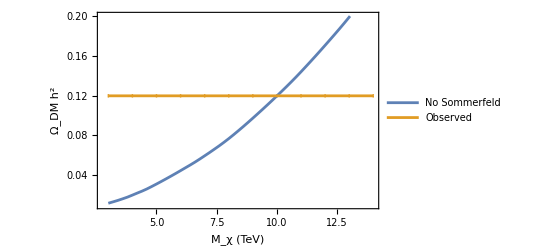

```mathematica
ListPlot[{ListSolution 1s1BS eff,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

#### Boltzmann RHS - with 1s3 BS (effective case)

```mathematica
ClearAll[σveff];σveff[i_] := σvHultenSESW[[i,2]]+σ0prime[MχList[[i]] TeV] (1/(BSF 1s TA List[[2]])+(gχ^2 σ0prime[MχList[[i]] TeV] (MχList[[i]] TeV)^2)/(2gI 1s[[2]] γI ann[[2]])(1/(4π z))^(3/2)Exp[-z EB1[MχList[[i]] TeV,BSqn[[2]],1,0,z]])^-1/.gχ->10;
```

```mathematica
ClearAll[χBoltzRHS BS eff,Solution BS eff];

χBoltzRHS BS eff = Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z]σveff[i] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) },{i,Length@MχList}];

Solution BS eff[i_]:={MχList[[i]] TeV,NDSolve[{D[YDM[z],z]==χBoltzRHS BS eff[[i,2]],YDM[zmin]==1.00001YDMEQ[MχList[[i]] TeV,zmin]},YDM,{z,zmin,zmax},Method->"StiffnessSwitching",AccuracyGoal->20][[1]]}//Quiet;
```

```mathematica
ListYields BS eff = Table[Solution BS eff[i],{i,1,Length@MχList}];//AbsoluteTiming
```

{25.9134,Null}

```mathematica
ListSolution 1s3BS eff = {ListYields BS eff[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYields BS eff[[All,2]]),ListYields BS eff[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolution 1s3BS eff][x] == 0.1198,{x,11}]

FindRoot[Interpolation[ListSolution 1s3BS eff][x] == 0.12,{x,11}]
```

{x→11.5725}

{x→11.5824}

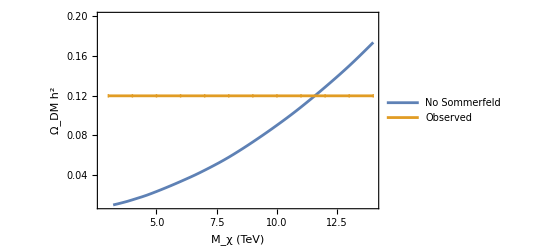

```mathematica
ListPlot[{ListSolution 1s3BS eff,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

#### Boltzmann RHS - with 1s5 BS (effective case)

```mathematica
ClearAll[σveff];σveff[i_] := σvHultenSESW[[i,2]]+σ0prime[MχList[[i]] TeV] (1/(BSF 1s TA List[[3]])+(gχ^2 σ0prime[MχList[[i]] TeV] (MχList[[i]] TeV)^2)/(2gI 1s[[3]] γI ann[[3]])(1/(4π z))^(3/2)Exp[-z EB1[MχList[[i]] TeV,BSqn[[3]],1,0,z]])^-1/.gχ->10;
```

```mathematica
ClearAll[χBoltzRHS BS eff,Solution BS eff];

χBoltzRHS BS eff = Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z]σveff[i] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) },{i,Length@MχList}];

Solution BS eff[i_]:={MχList[[i]] TeV,NDSolve[{D[YDM[z],z]==χBoltzRHS BS eff[[i,2]],YDM[zmin]==1.00001YDMEQ[MχList[[i]] TeV,zmin]},YDM,{z,zmin,zmax},Method->"StiffnessSwitching",AccuracyGoal->20][[1]]}//Quiet;
```

```mathematica
ListYields BS eff = Table[Solution BS eff[i],{i,1,Length@MχList}];//AbsoluteTiming
```

{25.3502,Null}

```mathematica
ListSolution 1s5BS eff = {ListYields BS eff[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYields BS eff[[All,2]]),ListYields BS eff[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolution 1s5BS eff][x] == 0.1198,{x,11}]

FindRoot[Interpolation[ListSolution 1s5BS eff][x] == 0.12,{x,11}]
```

{x→9.64374}

{x→9.65198}

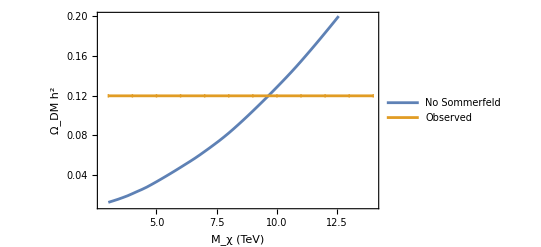

```mathematica
ListPlot[{ListSolution 1s5BS eff,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

#### Boltzmann RHS - with all 1s BS (effective case)

```mathematica
ClearAll[σveff];σveff[i_] := σvHultenSESW[[i,2]]+σ0prime[MχList[[i]] TeV] Sum[(1/(BSF 1s TA List[[j]])+(gχ^2 σ0prime[MχList[[i]] TeV] (MχList[[i]] TeV)^2)/(2gI 1s[[j]] γI ann[[j]])(1/(4π z))^(3/2)Exp[-z EB1[MχList[[i]] TeV,BSqn[[j]],1,0,z]])^-1/.gχ->10,{j,Length@BSF 1s TA List}];
```

```mathematica
ClearAll[χBoltzRHS BS eff,Solution BS eff];

χBoltzRHS BS eff = Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z]σveff[i] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) },{i,Length@MχList}];

Solution BS eff[i_]:={MχList[[i]] TeV,NDSolve[{D[YDM[z],z]==χBoltzRHS BS eff[[i,2]],YDM[zmin]==1.00001YDMEQ[MχList[[i]] TeV,zmin]},YDM,{z,zmin,zmax},Method->"StiffnessSwitching",AccuracyGoal->20][[1]]}//Quiet;
```

```mathematica
ListYields BS eff = Table[Solution BS eff[i],{i,1,Length@MχList}];//AbsoluteTiming
```

{31.9077,Null}

```mathematica
ListSolution 1sBS eff = {ListYields BS eff[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYields BS eff[[All,2]]),ListYields BS eff[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolution 1sBS eff][x] == 0.1198,{x,11}]

FindRoot[Interpolation[ListSolution 1sBS eff][x] == 0.12,{x,11}]
```

{x→12.0939}

{x→12.1044}

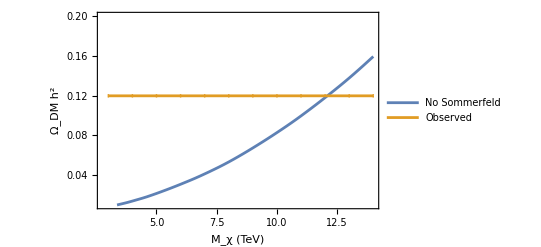

```mathematica
ListPlot[{ListSolution 1sBS eff,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

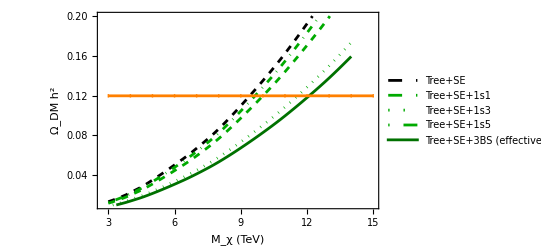

```mathematica
ListPlot[{ListSolutionHultenNoBS,ListSolution 1s1BS eff,ListSolution 1s3BS eff,ListSolution 1s5BS eff,ListSolution 1sBS eff,Table[{i,Around[.1198,.0017]},{i,3,15}]},
PlotStyle->{{Black,Dashed},{Darker@Green,Dashed},{Darker@Green,Dotted},{Darker@Green,DotDashed},Darker@Darker@Green,Orange},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"Tree+SE","Tree+SE+1s1","Tree+SE+1s3","Tree+SE+1s5","Tree+SE+3BS (effective)"}]
```

#### Boltzmann RHS - with 1s1 BS (network case)

```mathematica
ClearAll[χBoltzRHS BS full,YBSBoltzRHS BS full,Solution BS full];

χBoltzRHS BS full= Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z](σvMasslessSESW[[i,2]] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) +σ0prime[MχList[[i]] TeV]BSF 1s1 TA[z](YDM[z]^2 - Ys11[z] (Yratio[MχList[[i]] TeV,z][[1]])^-1))},{i,Length@MχList}];

YBSBoltzRHS BS full=Table[{MχList[[i]] TeV,
preFactor I[MχList[[i]] TeV,z]((ΓI break 1s NoExp[MχList[[i]] TeV,z][[1]]Yratio NoExp[MχList[[i]] TeV,z][[1]] YDM[z]^2-  ΓI break 1s[MχList[[i]] TeV,z][[1]]Ys11[z]) + Γann Huelten[MχList[[i]] TeV,z][[1]](YBSEQ[s11][MχList[[i]] TeV,z]-  Ys11[z])) },{i,Length@MχList}];
```

```mathematica
Solution BS full[i_]:={MχList[[i]] TeV,NDSolve[{
D[YDM[z],z]==χBoltzRHS BS full[[i,2]],
D[Ys11[z],z]==YBSBoltzRHS BS full[[i,2]],
YDM[zmin]==1.0001YDMEQ[MχList[[i]] TeV,zmin],
Ys11[zmin]==1.0001YBSEQ[s11][MχList[[i]] TeV,zmin]},
{YDM,Ys11},
{z,zmin,zmax},
Method->"StiffnessSwitching",AccuracyGoal->Automatic,WorkingPrecision->30,PrecisionGoal->16][[1]]};//Quiet
```

```mathematica
aa = Solution BS full[1];//Quiet//AbsoluteTiming
```

{2.0108,Null}

```mathematica
ListYields BS full = Table[Solution BS full[i],{i,1,Length@MχList,4}];//Quiet//AbsoluteTiming
```

{32.8799,Null}

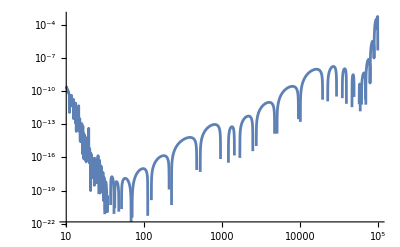

```mathematica
LogLogPlot[Ys11[z]/.aa[[2]],{z,zmin,(*10^4*)zmax},PlotRange->All]
```

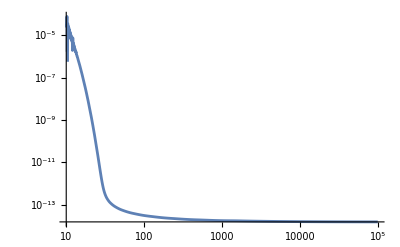

```mathematica
LogLogPlot[YDM[z]/.ListYields BS full[[2,2]],{z,zmin,(*10^4*)zmax},PlotRange->All]
```

```mathematica
ListSolution 1s1BS full = {ListYields BS full[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYields BS full[[All,2]]),ListYields BS full[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolution 1s1BS full][x] == 0.1198,{x,11}]
```

{x→9.97797}

```mathematica
FindRoot[Interpolation[ListSolution 1s1BS full][x] == 0.1198,{x,11}]
```

{x→10.1153}

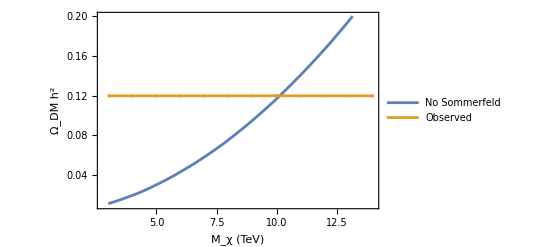

```mathematica
ListPlot[{ListSolution 1s1BS full,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

#### Boltzmann RHS - with 1s3 BS (network case)

```mathematica
ClearAll[χBoltzRHS BS full,YBSBoltzRHS BS full,Solution BS full];

χBoltzRHS BS full= Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z](σvMasslessSESW[[i,2]] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) +σ0prime[MχList[[i]] TeV]BSF 1s3 TA[z](YDM[z]^2 - Ys11[z] (Yratio[MχList[[i]] TeV,z][[2]])^-1))},{i,Length@MχList}];

YBSBoltzRHS BS full=Table[{MχList[[i]] TeV,
preFactor I[MχList[[i]] TeV,z](ΓI break 1s[MχList[[i]] TeV,z][[2]](Yratio[MχList[[i]] TeV,z][[2]] YDM[z]^2-  Ys11[z]) + Γann Huelten[MχList[[i]] TeV,z][[2]](YBSEQ[s13][MχList[[i]] TeV,z]-  Ys11[z])) },{i,Length@MχList}];
```

```mathematica
Solution BS full[i_]:={MχList[[i]] TeV,NDSolve[{
D[YDM[z],z]==χBoltzRHS BS full[[i,2]],
D[Ys11[z],z]==YBSBoltzRHS BS full[[i,2]],
YDM[zmin]==1.0001YDMEQ[MχList[[i]] TeV,zmin],
Ys11[zmin]==1.0001YBSEQ[s13][MχList[[i]] TeV,zmin]},
{YDM,Ys11},
{z,zmin,zmax},
Method->"StiffnessSwitching",(*AccuracyGoal->16,*)WorkingPrecision->30,PrecisionGoal->6][[1]]};//Quiet
```

```mathematica
aa = Solution BS full[1];//Quiet//AbsoluteTiming
```

{2.2598,Null}

```mathematica
ListYields BS full = Table[Solution BS full[i],{i,1,Length@MχList,2}];//Quiet//AbsoluteTiming
```

{88.4817,Null}

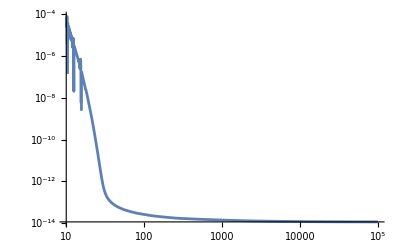

```mathematica
LogLogPlot[YDM[z]/.ListYields BS full[[2,2]],{z,zmin,zmax},PlotRange->All]
```

```mathematica
ListSolution 1s3BS full = {ListYields BS full[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYields BS full[[All,2]]),ListYields BS full[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolution 1s3BS full][x] == 0.1198,{x,11}]
```

{x→11.7443}

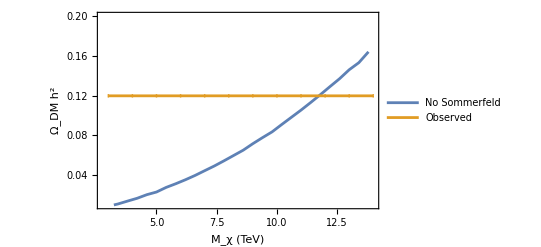

```mathematica
ListPlot[{ListSolution 1s3BS full,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

#### Boltzmann RHS - with 1s5 BS (network case)

```mathematica
ClearAll[χBoltzRHS BS full,YBSBoltzRHS BS full,Solution BS full];

χBoltzRHS BS full= Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z](σvMasslessSESW[[i,2]] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) +σ0prime[MχList[[i]] TeV]BSF 1s5 TA[z](YDM[z]^2 - Ys11[z] (Yratio[MχList[[i]] TeV,z][[3]])^-1))},{i,Length@MχList}];

YBSBoltzRHS BS full=Table[{MχList[[i]] TeV,
preFactor I[MχList[[i]] TeV,z](ΓI break 1s[MχList[[i]] TeV,z][[3]](Yratio[MχList[[i]] TeV,z][[3]] YDM[z]^2-  Ys11[z]) + Γann Huelten[MχList[[i]] TeV,z][[3]](YBSEQ[s15][MχList[[i]] TeV,z]-  Ys11[z])) },{i,Length@MχList}];
```

```mathematica
Solution BS full[i_]:={MχList[[i]] TeV,NDSolve[{
D[YDM[z],z]==χBoltzRHS BS full[[i,2]],
D[Ys11[z],z]==YBSBoltzRHS BS full[[i,2]],
YDM[zmin]==1.0001YDMEQ[MχList[[i]] TeV,zmin],
Ys11[zmin]==1.0001YBSEQ[s15][MχList[[i]] TeV,zmin]},
{YDM,Ys11},
{z,zmin,zmax},
Method->"StiffnessSwitching",(*AccuracyGoal->16,*)WorkingPrecision->35,PrecisionGoal->6][[1]]};//Quiet
```

```mathematica
aa = Solution BS full[1];//Quiet//AbsoluteTiming
```

{1.4793,Null}

```mathematica
ListYields BS full = Table[Solution BS full[i],{i,1,Length@MχList,2}];//Quiet//AbsoluteTiming
```

{50.0033,Null}

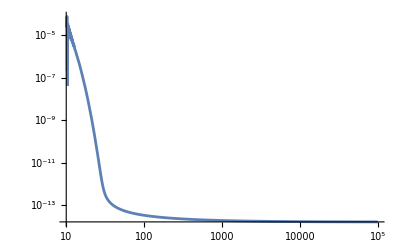

```mathematica
LogLogPlot[YDM[z]/.ListYields BS full[[2,2]],{z,zmin,(*10^4*)zmax},PlotRange->All]
```

```mathematica
ListSolution 1s5BS full = {ListYields BS full[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYields BS full[[All,2]]),ListYields BS full[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolution 1s5BS full][x] == 0.1198,{x,11}]
```

{x→9.6857}

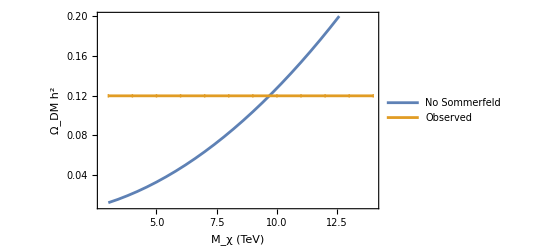

```mathematica
ListPlot[{ListSolution 1s5BS full,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

#### Boltzmann RHS - with all 1s BS (network case)

```mathematica
ClearAll[χBoltzRHS BS full,YBSBoltzRHS BS full,eqs,incond,Solution BS full];

χBoltzRHS BS full= Table[{MχList[[i]] TeV,preFactorσ[MχList[[i]] TeV,z](σvMasslessSESW[[i,2]] (YDM[z]^2 - YDMEQ[MχList[[i]] TeV,z]^2) +σ0prime[MχList[[i]] TeV]Sum[BSF 1s TA List[[j]](YDM[z]^2 - BSvar[[j]][z] (Yratio[MχList[[i]] TeV,z][[j]])^-1),
{j,Length@BSvar}])},{i,Length@MχList}];

YBSBoltzRHS BS full=Table[
Table[{MχList[[i]] TeV,
preFactor I[MχList[[i]] TeV,z](ΓI break 1s NoExp[MχList[[i]] TeV,z][[j]]Yratio NoExp[MχList[[i]] TeV,z][[j]] YDM[z]^2-  ΓI break 1s[MχList[[i]] TeV,z][[j]]BSvar[[j]][z] + Γann Huelten[MχList[[i]] TeV,z][[j]](YBSEQ[s11][MχList[[i]] TeV,z]-  BSvar[[j]][z])) },{i,Length@MχList}],
{j,Length@BSvar}];

eqs[i_] := {D[YDM[z],z]==χBoltzRHS BS full[[i,2]]}~Join~Table[D[BSvar[[j]][z],z]==YBSBoltzRHS BS full[[j,i,2]],{j,Length@BSvar}];

incond[i_] := {YDM[zmin]==1.0001YDMEQ[MχList[[i]] TeV,zmin]}~Join~Table[BSvar[[j]][zmin]==1.0001YBSEQ[BSqn[[j]]][MχList[[i]] TeV,zmin],{j,Length@BSvar}];
```

```mathematica
Solution BS full[i_]:={MχList[[i]] TeV,
NDSolve[eqs[i]~Join~incond[i],
Flatten@{YDM,BSvar},
{z,zmin,zmax},
Method->"StiffnessSwitching",AccuracyGoal->Automatic,WorkingPrecision->35,PrecisionGoal->16][[1]]};//Quiet
```

```mathematica
aa = Solution BS full[1];//Quiet//AbsoluteTiming
```

{8.73688,Null}

```mathematica
ListYields BS full = Table[Solution BS full[i],{i,1,Length@MχList,4}];//Quiet//AbsoluteTiming
```

{130.728,Null}

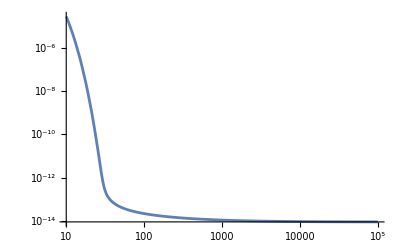

```mathematica
LogLogPlot[YDM[z]/.aa[[2]],{z,zmin,zmax},PlotRange->All]
```

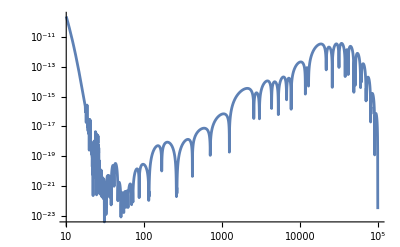

```mathematica
LogLogPlot[Abs@Ys11[z]/.ListYields BS full[[2,2]],{z,zmin,zmax},PlotRange->All]
```

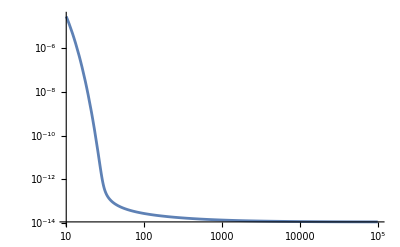

```mathematica
LogLogPlot[YDM[z]/.ListYields BS full[[2,2]],{z,zmin,zmax},PlotRange->All]
```

```mathematica
YDM[zmax]/.ListYields BS full[[All,2]];
YDM[zmax/10]/.ListYields BS full[[All,2]];
%/%%
```

{1.033729719140063175884865984962145,1.035778564874046003499950253174602,1.037358299612908480978825818391906,1.038554956832629205458353151072945,1.039455775594867895403848048854069,1.040092736376777784387502828372382,1.040699232884702155908778052731947,1.040970417243297927215432700300672,1.041553622313971754720440229442012,1.04157538303863310633446068553426,1.042076949877483909433578706404941,1.04214348256949637969576804873968,1.042420141541099554661540341225828,1.042785154488962616172616147570775}

```mathematica
ListSolution 1sBS full = {ListYields BS full[[All,1]]/TeV,ΩDM[1,(YDM[zmax]/.ListYields BS full[[All,2]]),ListYields BS full[[All,1]]]}//Transpose;
```

```mathematica
FindRoot[Interpolation[ListSolution 1sBS full][x] == 0.1198,{x,11}]
```

{x→12.2976}

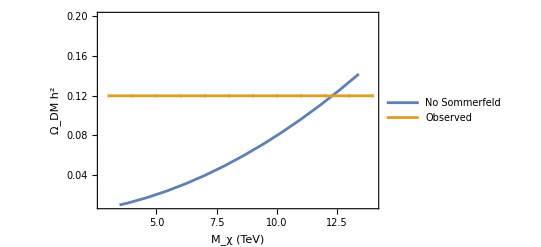

```mathematica
ListPlot[{ListSolution 1sBS full,Table[{i,Around[.1198,.0017]},{i,3,14}]},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"No Sommerfeld","Observed"}]
```

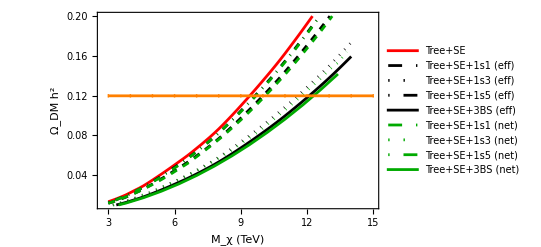

```mathematica
ListPlot[{ListSolutionHultenNoBS,ListSolution 1s1BS eff,ListSolution 1s3BS eff,ListSolution 1s5BS eff,ListSolution 1sBS eff,ListSolution 1s1BS full,ListSolution 1s3BS full,ListSolution 1s5BS full,ListSolution 1sBS full,Table[{i,Around[.1198,.0017]},{i,3,15}]},
PlotStyle->{Red,{Black,Dashed},{Black,Dotted},{Black,DotDashed},Black,{Darker@Green,Dashed},{Darker@Green,Dotted},{Darker@Green,DotDashed},Darker@Green,Orange},PlotRange->{All,{0.01,0.2}},Evaluate[MyOptions],FrameLabel->{"M_χ (TeV)","Ω_DM h^2"},Joined->True,PlotLegends->{"Tree+SE","Tree+SE+1s1 (eff)","Tree+SE+1s3 (eff)","Tree+SE+1s5 (eff)","Tree+SE+3BS (eff)","Tree+SE+1s1 (net)","Tree+SE+1s3 (net)","Tree+SE+1s5 (net)","Tree+SE+3BS (net)"}]
```

```mathematica
ll={{ListSolution 1s1BS eff,ListSolution 1s1BS full},{ListSolution 1s3BS eff,ListSolution 1s3BS full},{ListSolution 1s5BS eff,ListSolution 1s5BS full},{ListSolution 1sBS eff,ListSolution 1sBS full}};
```

```mathematica
llm=Map[(x/.FindRoot[Interpolation[#][x] == 0.1198,{x,11}] &),ll,{2}]//Quiet
```

{{10.0026,10.1062},{11.5725,11.7443},{9.64374,9.6857},{12.0939,12.2977}}

```mathematica
Table[{{"1s1","1s3","1s5","all 1s"}[[i]],llm[[i,1]],llm[[i,2]],Abs[1-llm[[i,1]]/llm[[i,2]] ]100},{i,4}]//TraditionalForm
```

(1s1 | 10.0026 | 10.1062 | 1.02528
1s3 | 11.5725 | 11.7443 | 1.46276
1s5 | 9.64374 | 9.6857 | 0.433247
all 1s | 12.0939 | 12.2977 | 1.65758)

```mathematica
(1 - 12.4/12.6) 100
(1 - 12.09/12.297) 100
```

1.5873

1.68334

## Solve Schroedinger equation for Yukawa potential

```mathematica
ClearAll[VYukawa,Schroedinger,BoundaryConditions];

VYukawa[Mχ_,z_,{Isp_,n_},x_,MV_]:=(-αeff[{Isp,n},Mχ,z]Exp[-MV[Mχ/z]/Mχ x])/x;

Schroedinger[Mχ_,z_,{Isp_,n_},x_,MV_,ell_,vrel_]:=-D[ul[x],{x,2}] + (VYukawa[Mχ,z,{Isp,n},x,MV] + (ell (ell + 1))/x^2 - vrel^2/4)  ul[x]==0;

BoundaryConditions[Mχ_,vrel_,rInf_,r0_]:={(D[ul[x],x] - I Mχ vrel ul[x]/.x->rInf) == √(4 π) Exp[I Mχ vrel rInf],(ul[x]/.x->r0)==0};
```

```mathematica
Schr0WSU2[Mχ_,z_,{Isp_,n_},x_]:=Schroedinger[Mχ,z,{Isp,n},x,MWTSU2,0,vM[Mχ]];
```

```mathematica
{Schr0WSU2[3 TeV,1000,Qs1,x]/.l->Log@40.}~Join~BoundaryConditions[10 TeV,vM[10 TeV],rInf,r0]/.l->Log@4.
```

{(-0.224377-(0.219171 ⅇ^(-0.0267883 x))/x) ul[x]-ul''[x]==0,(0.+0. ⅈ)+ul'[100]==3.54491+0. ⅈ,ul[0]==0}

```mathematica
Log@4.//N
```

1.38629

```mathematica
ClearAll[lTA]
```

```mathematica
rInf = 200;r0=0.01;
(*lTA =Log@4.;*)aa = Table[NDSolve[{Schr0WSU2[10 TeV,10,Qs1,x]/.l->lTA}~Join~BoundaryConditions[10 TeV,vM[10 TeV],rInf,r0]/.l->lTA,ul,
{x,r0,rInf}(*,Method->"StiffnessSwitching"*)][[1]], {lTA,Log@4.,20}];
```

```mathematica
(1/(√(4π)))D[ul[x],x]/.aa/.x->r0//Total//Abs
```

6.03424

```mathematica
Abs[(1/(√(4π)))D[ul[y],y]/.aa]
```

Abs[InterpolatingFunction[…][y]]/(2 √π)

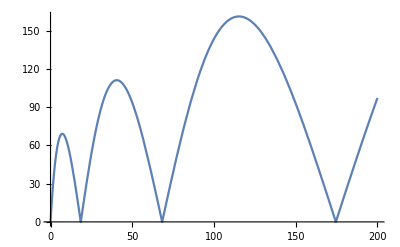

```mathematica
Plot[Abs@ul[x]/.aa,{x,r0,rInf}]
```

```mathematica
Abs@(ul[rInf]/ul[r0])/.aa
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

∞

```mathematica
10 TeV
```